# Integrais para o Matheus

## Inicialização

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

```mathematica
SetOptions[{Plot,LogPlot,LogLinearPlot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,Axes-> False,Frame-> True];
```

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,Joined->True,Axes-> False,Frame-> True];
```

```mathematica
u[h_]:=NIntegrate[1/Sqrt[(1-(Sin[h]^2)Sin[x]^2)(1-(2*9.81*100000/300000000^2)(Sin[h]^2)(Cos[x]^2)-2/3((2*9.81*100000/300000000^2)^2)(Sin[h]^4)(Cos[x]^4)-1/3((2*9.81*100000/300000000^2)^3)(Sin[h]^6)(Cos[x]^6))],{x,0,π/2}]
```

```mathematica
v[h_]:=NIntegrate[1/Sqrt[1-Sin[h]^2Sin[x]^2],{x,0,π/2}]
```

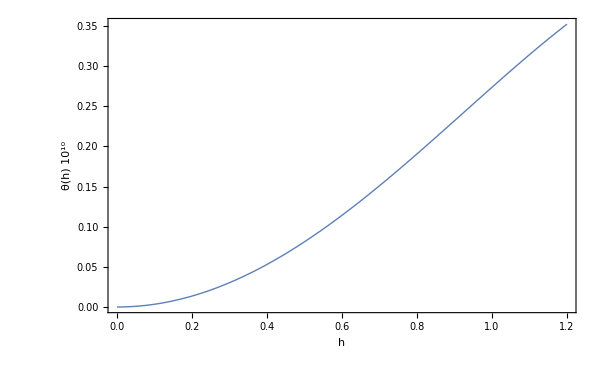

```mathematica
obj=Plot[4 10^10(u[h]-v[h]),{h,0,1.2}, FrameLabel->{"h", "θ(h) 10^10 "}]
```

```mathematica
Export["graf.pdf", obj]
```

graf.pdf